```mathematica
data=Import["~/workspace/wikigraph/data/wikidataout/wikiprofile.noip.vector.csv"];
```

```mathematica
Length[data]
```

999837

```mathematica
Length[data[[2]]]
```

19

```mathematica
trdata=Transpose[data];
```

```mathematica
Length[trdata[[1]]]
```

999837

```mathematica
trdata[[1]][[1;;10]]
```

{id,0,1,2,3,4,5,6,7,8}

```mathematica
limit = .93
```

0.93

```mathematica
Map[Function[x,{x[[1]],Min[x[[2;;]]]}],trdata]
```

{{id,0},{nedits,2},{narticles,1},{daysactive,2},{naddedits,0},{nremoveedits,0},{bytesadded,0},{bytesremoved,0},{avgeditsday,0.0004},{avgarticlesday,0.0002},{avgtimetonext,0.},{avgbytesadded,0},{avgbytesremoved,0},{netbytes,-11423784},{avgnetbytes,-95917.3},{articlensedits,0},{adminnsedits,0},{pctarticlensedits,0},{pctadminnsedits,0}}

```mathematica
Map[Function[x,{x[[1]],Max[x[[2;;]]]}],trdata]
```

{{id,999835},{nedits,3008950},{narticles,2504647},{daysactive,4571},{naddedits,2949526},{nremoveedits,135820},{bytesadded,1793038869},{bytesremoved,301961193},{avgeditsday,1486.02},{avgarticlesday,1311.33},{avgtimetonext,3633.5},{avgbytesadded,2.40006×10^6},{avgbytesremoved,1.26337×10^6},{netbytes,1790307455},{avgnetbytes,2.40006×10^6},{articlensedits,2842613},{adminnsedits,683585},{pctarticlensedits,1},{pctadminnsedits,1}}

nedits

3008950

2

{}

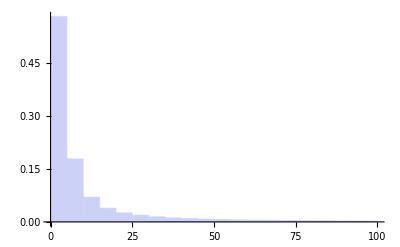

```mathematica
trdata[[2,1]]
d = trdata[[2]][[2;;]];
Max[d]
Min[d]
h = HistogramList[d,{25},"CDF"];
Select[Transpose[{h[[1]][[2;;]],h[[2]]}],#[[2]]>limit&,10]
Histogram[d,{0,100,5},"Probability"]
```

narticles

{{200,0.956273},{250,0.962224},{300,0.966499},{350,0.969693},{400,0.972236},{450,0.97436},{500,0.976036},{550,0.977507},{600,0.97873},{650,0.979855}}

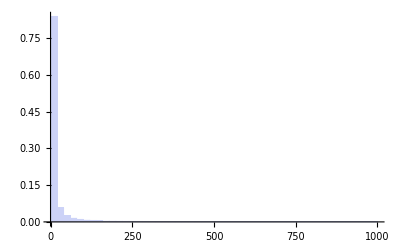

```mathematica
trdata[[3,1]]
d = trdata[[3]][[2;;]];
h = HistogramList[d,{50},"CDF"];
Select[Transpose[{h[[1]][[2;;]],h[[2]]}],#[[2]]>limit&,10]
Histogram[d,{0,1000,20},"Probability"]
```

daysactive

{{3,0.0157896},{4,0.0291478},{5,0.0414208},{6,0.0523546},{7,0.0627463},{8,0.0726169},{9,0.0813603},{10,0.0893717},{11,0.0968829},{12,0.103877}}

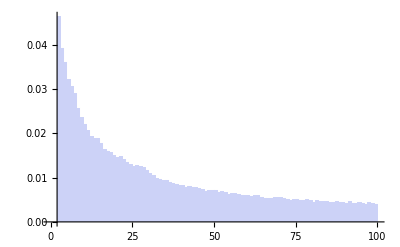

```mathematica
trdata[[4,1]]
d = trdata[[4]][[2;;]];
h = HistogramList[d,{1},"CDF"];
Select[Transpose[{h[[1]][[2;;]],h[[2]]}],#[[2]]≥.009&,10]
Histogram[d,{0,100,1},"Probability"]
```

naddedits

{{2,0.00988362},{3,0.357911},{4,0.454765},{5,0.540346},{6,0.589129},{7,0.629745},{8,0.658935},{9,0.683458},{10,0.703205},{11,0.719822}}

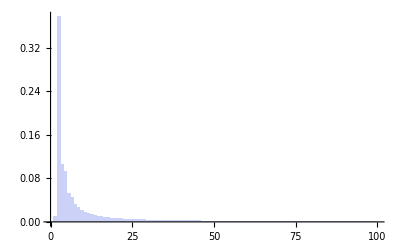

```mathematica
trdata[[5,1]]
d = trdata[[5]][[2;;]];
h = HistogramList[d,{1},"CDF"];
Select[Transpose[{h[[1]][[2;;]],h[[2]]}],#[[2]]>.001&,10]
Histogram[d,{0,100,1},"Probability"]
```

```mathematica
Select[Transpose[{h[[1]][[2;;]],h[[2]]}],#[[2]]>.0001&,10]
```

{{10,0.703205},{20,0.802361},{30,0.843179},{40,0.866842},{50,0.882917},{60,0.894833},{70,0.903997},{80,0.911352},{90,0.917434},{100,0.92254}}

nremoveedits

{{3,0.948541},{4,0.95904},{5,0.965266},{6,0.969527},{7,0.9727},{8,0.975165},{9,0.977088},{10,0.978732},{11,0.980063},{12,0.981244}}

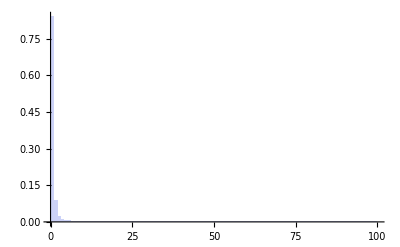

```mathematica
trdata[[6,1]]
d = trdata[[6]][[2;;]];
h = HistogramList[d,{1},"CDF"];
Select[Transpose[{h[[1]][[2;;]],h[[2]]}],#[[2]]>limit&,10]
Histogram[d,{0,100,1},"Probability"]
```

bytesadded

{{30000,0.939053},{40000,0.949038},{50000,0.95545},{60000,0.959869},{70000,0.963342},{80000,0.965981},{90000,0.968139},{100000,0.969982},{110000,0.971538},{120000,0.972925}}

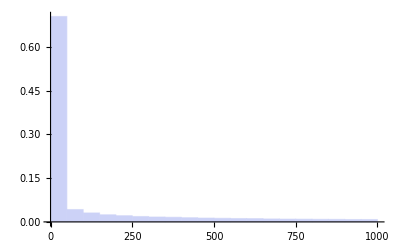

```mathematica
trdata[[7,1]]
d = trdata[[7]][[2;;]];
h = HistogramList[d,{10000},"CDF"];
Select[Transpose[{h[[1]][[2;;]],h[[2]]}],#[[2]]>limit&,10]
Histogram[d,{0,1000,50},"Probability"]
```

bytesremoved

{{500,0.933785},{750,0.941532},{1000,0.94671},{1250,0.950716},{1500,0.953911},{1750,0.956463},{2000,0.958787},{2250,0.960615},{2500,0.962252},{2750,0.963771}}

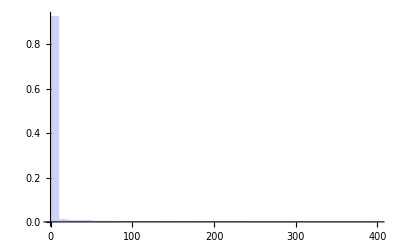

```mathematica
trdata[[8,1]]
d = trdata[[8]][[2;;]];
h = HistogramList[d,{250},"CDF"];
Select[Transpose[{h[[1]][[2;;]],h[[2]]}],#[[2]]>limit&,10]
Histogram[d,{0,400,10},"Probability"]
```

avgeditsday

{{0.52,0.939718},{0.54,0.940632},{0.56,0.941649},{0.58,0.942855},{0.6,0.943562},{0.62,0.945618},{0.64,0.946445},{0.66,0.946965},{0.68,0.959222},{0.7,0.9597}}

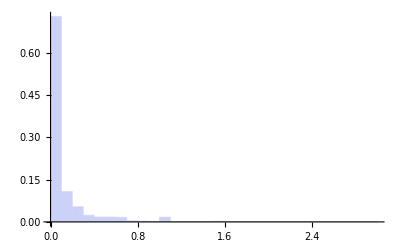

```mathematica
trdata[[9,1]]
d = trdata[[9]][[2;;]];
h = HistogramList[d,{.02},"CDF"];
Select[Transpose[{h[[1]][[2;;]],h[[2]]}],#[[2]]>limit&,10]
Histogram[d,{0,3,.1},"Probability"]
```

avgarticlesday

{{0.46,0.940235},{0.47,0.940701},{0.48,0.941125},{0.49,0.941509},{0.5,0.941801},{0.51,0.954378},{0.52,0.954691},{0.53,0.95503},{0.54,0.955374},{0.55,0.955735}}

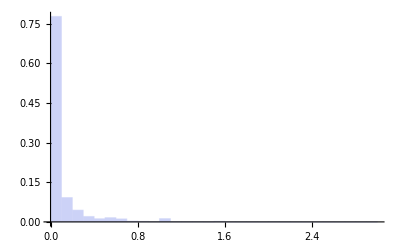

```mathematica
trdata[[10,1]]
d = trdata[[10]][[2;;]];
h = HistogramList[d,{.01},"CDF"];
Select[Transpose[{h[[1]][[2;;]],h[[2]]}],#[[2]]>.94&,10]
Histogram[d,{0,3,.1},"Probability"]
```

avgtimetonext

{{188,0.950318},{190,0.951107},{192,0.951836},{194,0.952594},{196,0.953302},{198,0.953999},{200,0.954679},{202,0.955388},{204,0.956067},{206,0.956713}}

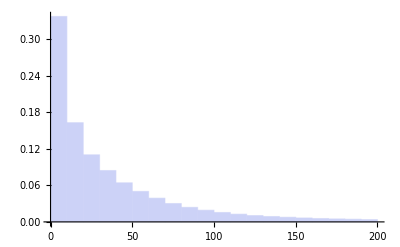

```mathematica
trdata[[11,1]]
d = trdata[[11]][[2;;]];
h = HistogramList[d,Automatic,"CDF"];
Select[Transpose[{h[[1]][[2;;]],h[[2]]}],#[[2]]>.95&,10]
Histogram[d,{0,200,10},"Probability"]
```

avgbytesadded

{{1600,0.931674},{1700,0.936385},{1800,0.940577},{1900,0.944496},{2000,0.948019},{2100,0.951126},{2200,0.954062},{2300,0.956758},{2400,0.959201},{2500,0.961442}}

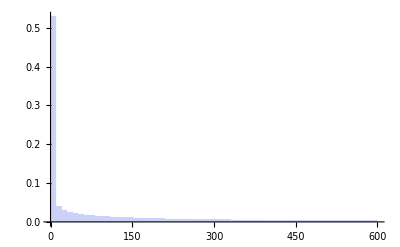

```mathematica
trdata[[12,1]]
d = trdata[[12]][[2;;]];
h = HistogramList[d,Automatic,"CDF"];
Select[Transpose[{h[[1]][[2;;]],h[[2]]}],#[[2]]>limit&,10]
Histogram[d,{0,600,10},"Probability"]
```

avgbytesremoved

{{200,0.93111},{300,0.941592},{400,0.948876},{500,0.954196},{600,0.958463},{700,0.961851},{800,0.96476},{900,0.967246},{1000,0.969424},{1100,0.971296}}

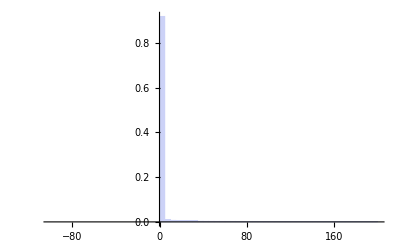

```mathematica
trdata[[13,1]]
d = trdata[[13]][[2;;]];
h = HistogramList[d,Automatic,"CDF"];
Select[Transpose[{h[[1]][[2;;]],h[[2]]}],#[[2]]>limit&,10]
Histogram[d,{-100,200,5},"Probability"]
```

```mathematica
sd[[1]]
```

1790307455

netbytes

{{-13000,0.0011},{-12500,0.0011},{-12000,0.0012},{-11500,0.0012},{-11000,0.0013},{-10500,0.0013},{-10000,0.0013},{-9500,0.0013},{-9000,0.0013},{-8500,0.0014},{-8000,0.0014},{-7500,0.0014},{-7000,0.0014},{-6500,0.0014},{-6000,0.0017},{-5500,0.002},{-5000,0.0023},{-4500,0.0024},{-4000,0.0027},{-3500,0.0028}}

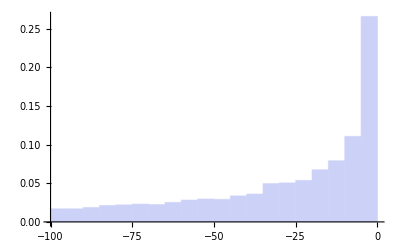

```mathematica
trdata[[14,1]]
d = trdata[[14]][[2;;]];
h = HistogramList[RandomSample[d,10000],{-11450000,1790307455,500},"CDF"];
Select[Transpose[{h[[1]][[2;;]],h[[2]]}],#[[2]]>.001&,20]
Histogram[d,{-100,0,5},"Probability"]
```

```mathematica
Select[Transpose[{h[[1]][[2;;]],h[[2]]}],#[[2]]>.001&,50]
```

{{-13000,0.0011},{-12500,0.0011},{-12000,0.0012},{-11500,0.0012},{-11000,0.0013},{-10500,0.0013},{-10000,0.0013},{-9500,0.0013},{-9000,0.0013},{-8500,0.0014},{-8000,0.0014},{-7500,0.0014},{-7000,0.0014},{-6500,0.0014},{-6000,0.0017},{-5500,0.002},{-5000,0.0023},{-4500,0.0024},{-4000,0.0027},{-3500,0.0028},{-3000,0.0032},{-2500,0.0035},{-2000,0.0039},{-1500,0.0048},{-1000,0.0057},{-500,0.0082},{0,0.0291},{500,0.5503},{1000,0.6094},{1500,0.65},{2000,0.6839},{2500,0.7111},{3000,0.7321},{3500,0.7508},{4000,0.7688},{4500,0.7808},{5000,0.7954},{5500,0.8074},{6000,0.8204},{6500,0.8285},{7000,0.8371},{7500,0.8457},{8000,0.8543},{8500,0.8597},{9000,0.8655},{9500,0.8705},{10000,0.8747},{10500,0.8799},{11000,0.8835},{11500,0.8873}}

avgnetbytes

{{-1200,0.00104817},{-1100,0.00117419},{-1000,0.00128821},{-900,0.00142924},{-800,0.00160727},{-700,0.0018263},{-600,0.00210235},{-500,0.0024534},{-400,0.00296549},{-300,0.00368461},{-200,0.00497582},{-100,0.00746723},{0,0.030574},{100,0.611668},{200,0.694339},{300,0.747228},{400,0.784866},{500,0.813064},{600,0.835472},{700,0.853489}}

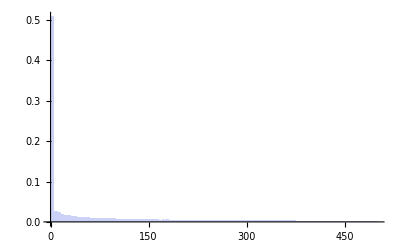

```mathematica
trdata[[15,1]]
d = trdata[[15]][[2;;]];
h = HistogramList[d,{-96000,2400000,100},"CDF"];
Select[Transpose[{h[[1]][[2;;]],h[[2]]}],#[[2]]>.001&,20]
Histogram[d,{0,500,5},"Probability"]
```

articlensedits

{{2000,0.990704},{2200,0.991387},{2400,0.991992},{2600,0.992492},{2800,0.992952},{3000,0.993342},{3200,0.993725},{3400,0.994034},{3600,0.99431},{3800,0.99459},{4000,0.994844},{4200,0.995073},{4400,0.99529},{4600,0.995485},{4800,0.995669},{5000,0.995846},{5200,0.996004},{5400,0.996176},{5600,0.996334},{5800,0.996446}}

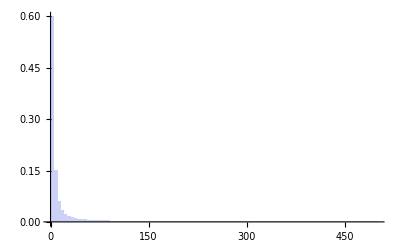

```mathematica
trdata[[16,1]]
d = trdata[[16]][[2;;]];
h = HistogramList[d,Automatic,"CDF"];
Select[Transpose[{h[[1]][[2;;]],h[[2]]}],#[[2]]>.99&,20]
Histogram[d,{0,500,5},"Probability"]
```

adminnsedits

{{350,0.990149},{400,0.991017},{450,0.991723},{500,0.99232},{550,0.992829},{600,0.993258},{650,0.993674},{700,0.994031},{750,0.994348},{800,0.994647},{850,0.994906},{900,0.995133},{950,0.995357},{1000,0.995564},{1050,0.995751},{1100,0.995913},{1150,0.996054},{1200,0.996194},{1250,0.996338},{1300,0.996457}}

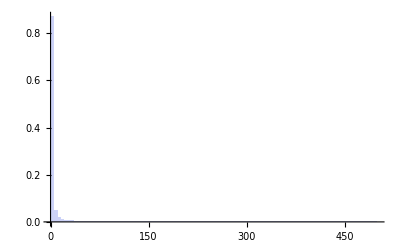

```mathematica
trdata[[17,1]]
d = trdata[[17]][[2;;]];
h = HistogramList[d,Automatic,"CDF"];
Select[Transpose[{h[[1]][[2;;]],h[[2]]}],#[[2]]>.99&,20]
Histogram[d,{0,500,5},"Probability"]
```

pctarticlensedits

{{0.935,0.906563},{0.94,0.915356},{0.945,0.92587},{0.95,0.933043},{0.955,0.943564},{0.96,0.951247},{0.965,0.96035},{0.97,0.968498},{0.975,0.97575},{0.98,0.982854},{0.985,0.989079},{0.99,0.994126},{0.995,0.998111},{1.,1.}}

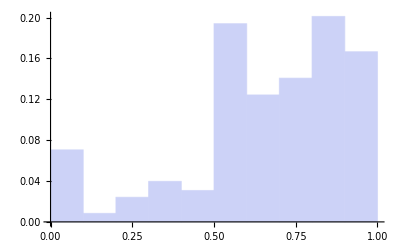

```mathematica
trdata[[18,1]]
d = trdata[[18]][[2;;]];
h = HistogramList[d,{.005},"CDF"];
Select[Transpose[{h[[1]][[2;;]],h[[2]]}],#[[2]]>.90&,20]
Histogram[d,{0,1,.1},"Probability"]
```

pctadminnsedits

{{0.67,0.986152},{0.675,0.98622},{0.68,0.986318},{0.685,0.986478},{0.69,0.98664},{0.695,0.986869},{0.7,0.986943},{0.705,0.987356},{0.71,0.987498},{0.715,0.988481},{0.72,0.988547},{0.725,0.988655},{0.73,0.988918},{0.735,0.989079},{0.74,0.989186},{0.745,0.989246},{0.75,0.989267},{0.755,0.993536},{0.76,0.993597},{0.765,0.993728}}

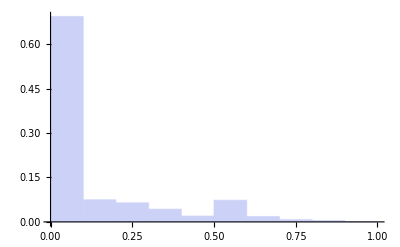

```mathematica
trdata[[19,1]]
d = trdata[[19]][[2;;]];
h = HistogramList[d,{.005},"CDF"];
Select[Transpose[{h[[1]][[2;;]],h[[2]]}],#[[2]]>.98&,20]
Histogram[d,{0,1,.1},"Probability"]
```

```mathematica
Select[Transpose[{h[[1]][[2;;]],h[[2]]}],#[[2]]>.97&,20]
```

{{0.82,0.970105},{0.83,0.970228},{0.84,0.97115},{0.85,0.971292},{0.86,0.971818},{0.87,0.971934},{0.88,0.972243},{0.89,0.972499},{0.9,0.972563},{0.91,0.972831},{0.92,0.972941},{0.93,0.973059},{0.94,0.973153},{0.95,0.973221},{0.96,0.973276},{0.97,0.973335},{0.98,0.973362},{0.99,0.973393},{1.,0.97342},{1.01,1.}}

```mathematica
sd = Sort[trdata[[15]][[2;;]]];
sd[[1]]
```

-95917.3

```mathematica
outlierprcounts=ReadList["~/workspace/wikigraph/data/wikidataout/prdata/wikiprofile.noip.out.prcount",{Number,Number}];
```

```mathematica
neditsprcounts = ReadList["~/workspace/wikigraph/data/wikidataout/prdata/wikiprofile.noip.out.nedit.prcount",{Number,Number}];
```

```mathematica
articlenserrorprcount = ReadList["~/workspace/wikigraph/data/wikidataout/prdata/articlesnserror.sort3.prcount",{Number,Number}];
```

```mathematica
neditserrorsprcount= ReadList["~/workspace/wikigraph/data/wikidataout/prdata/neditserrors.sort3.prcount",{Number,Number}];
```

```mathematica
pctadminerrorsprcount= ReadList["~/workspace/wikigraph/data/wikidataout/prdata/pctadminerrors.sort1.prcount",{Number,Number}];
```

```mathematica
samplesize = 200000;
Export["precisionrecall.png",ListPlot[
{Sort[RandomSample[outlierprcounts,samplesize]],
Sort[RandomSample[neditsprcounts,samplesize]],
Sort[RandomSample[articlenserrorprcount,samplesize]],
Sort[RandomSample[neditserrorsprcount,samplesize]],
Sort[RandomSample[pctadminerrorsprcount,samplesize]]},
PlotRange->{{0,.4},{0,1}},
PlotStyle->{{Red},{Orange},{Blue},{Black},{Purple}},
PlotLegends->Placed[LineLegend[{"score","edits","articlens-error","nedits-error","pctadmin-error"},LabelStyle->{FontWeight->"Bold",FontSize->8}],Top],
Joined->{True,True,True,True,True},
AxesLabel->{"Recall","Precision"},
BaseStyle->{FontSize->8}
],ImageSize->500]
```

precisionrecall.png

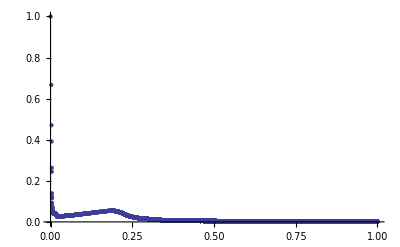

```mathematica
prcountsort=ReadList["~/workspace/wikigraph/data/wikidataout/prdata/wikiprofile.noip.out.prcount",{Number,Number}];
ListPlot[RandomSample[prcountsort,100000],PlotRange->{{0,1},{0,1}}]
```

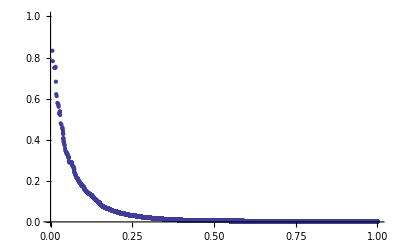

```mathematica
prcountsort=ReadList["~/workspace/wikigraph/data/wikidataout/prcountsort.out",{Number,Number}];
ListPlot[RandomSample[prcountsort,100000],PlotRange->{{0,1},{0,1}}]
```

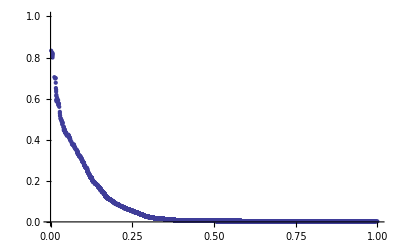

```mathematica
prcountsort=ReadList["~/workspace/wikigraph/data/wikidataout/prcounts.neditserrors.raw",{Number,Number}];
ListPlot[RandomSample[prcountsort,200000],PlotRange->{{0,1},{0,1}},ImageSize->Full]
```

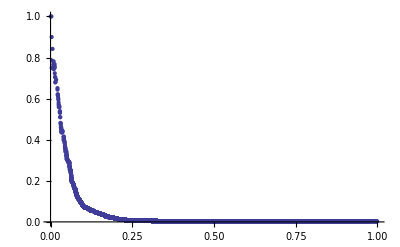

-Graphics-

```mathematica
prcountsort=ReadList["~/workspace/wikigraph/data/wikidataout/prcountarticlenserror.out",{Number,Number}];
ListPlot[RandomSample[prcountsort,200000],PlotRange->{{0,1},{0,1}},ImageSize->Full]
```